# K and WF

## From Irinas script ‘RandomLatticeTG_ShortMoveOut_mod’

Define things

## System parameters

```mathematica
numBar=5; (* Total number of the delta barriers*)
ys = Symbol["y"<>ToString[#]]&/@Range[1,numBar] (*List of the variables (placeholders) for the positions of the barriers*)
ds=Symbol["d"<>ToString[#]]&/@Range[1,numBar](*List of the variables (placeholders) for the heights of the barriers*)
specificRules = {L->10, ℏ->1, m->1}; (*Rules to fix the length of the box L, and the ℏ/m ratio*)
$Assumptions=Element[ds, Reals]&&Element[ys, Reals]&&Element[L, Reals] &&Element[m, Reals]&& Element[ℏ, Reals]&&Element[k, Reals](*General assumptions about parameters. They are all real.*)
```

{y1,y2,y3,y4,y5}

{d1,d2,d3,d4,d5}

(d1|d2|d3|d4|d5)∈Reals&&(y1|y2|y3|y4|y5)∈Reals&&L∈Reals&&m∈Reals&&ℏ∈Reals&&k∈Reals

## Cyclic permutation barrier heights

```mathematica
cyclicBarrierShiftHeights[Δ_, ys_, ds_, L_]:=Module[{shift, signs, dels, resultDs, Nb},(Nb = Length[ds];dels=Flatten[{L/2-#&/@ Reverse[ys], L}];signs=Sign[Mod[Δ,L] - dels]; shift=Floor[Total[signs + 1]/2];resultDs = Flatten[{ds[[Nb-shift+1;;Nb]],ds[[1;;Nb-shift]]}])]
(* Cyclic permutation of the barrier positions *)
cyclicBarrierShiftPos[Δ_, ys_, L_]:=Module[{Nb, resultYs},(Nb = Length[ds];resultYs = Sort[Mod[ys+Δ + L/2, L]-L/2])]
```

## Bethe Equations

```mathematica
𝒯[n_, ys_, ds_]:= Module[{combs},(combs=Subsets[Range[1,Length[ys]], {n}];2^(2n)Total[Times@@(ds[[#]] m/ℏ^2)If[Length[#]>=1, Sin[k(ys[[#]][[1]]+L/2)]Sin[k(L/2-ys[[#]][[n]])], Sin[k L]]Product[Sin[k(ys[[#]][[j]]-ys[[#]][[j-1]])],{j,2,n}]&/@combs])]
𝒯[1, ys, ds];
```

```mathematica
makeBE[ys_, ds_]:=Sum[𝒯[n, ys, ds] k^(Length[ds]-n), {n, 0, Length[ds]}]==0
AbsoluteTiming[TGBE=makeBE[ys, ds];]
```

{0.002605,Null}

## Normalization coefficients

```mathematica
(*n is the number of the well in which the particle is in, for 1-particle case. The coefficient we are calculating is Subscript["𝒜", {1,0,0,0,0}][{k1}], with 1 in the well number n.  ds - heights of the barriers, ys - positions of the barriers*)
makeCoef[n_, ds_, ys_]:=Module[{combs, posCombs, elems, curProd, curYP},(combs=Subsets[Range[1,n-1], n-1]; elems = Total[(Times@@(ds[[#]]*(-2 m ⅈ)/(k ℏ^2))If[Length[#]>0,(1-Exp[-ⅈ k (L + 2 ys[[#]][[1]])]), 1])Product[(1-Exp[-ⅈ 2 k (+ys[[#]][[j]]-ys[[#]][[j-1]])]), {j, 2, Length[#]}]&/@combs])];
makeCoef[2, ds, ys];
```

### Real Part

```mathematica
realPartMakeCoef[n_, ds_, ys_]:=Module[{combs, posCombs, elems, curProd, curYP},(combs=Subsets[Range[1,n-1], n-1]; elems = Total[(Times@@(ds[[#]])((-4 m)/(k ℏ^2))^Length[#] If[Length[#]>0,(-Sin[k(L/2+ys[[#]][[1]])]Cos[k(ys[[#]][[Length[#]]]+L/2)]), 1])Product[(Sin[ k (-ys[[#]][[j]]+ys[[#]][[j-1]])]), {j, 2, Length[#]}]&/@combs])];
realPartMakeCoef[2, ds, ys];
```

### Im Part

```mathematica
imPartMakeCoef[n_, ds_, ys_]:=Module[{combs, posCombs, elems, curProd, curYP},(combs=Subsets[Range[1,n-1], {1,n-1}]; elems = Total[(Times@@(ds[[#]])((-4 m)/(k ℏ^2))^Length[#] If[Length[#]>0,(Sin[k(L/2+ys[[#]][[1]])]Sin[k(ys[[#]][[Length[#]]]+L/2)]), 1])Product[(Sin[ k (-ys[[#]][[j]]+ys[[#]][[j-1]])]), {j, 2, Length[#]}]&/@combs])];
imPartMakeCoef[2, {d1,d2,d3}, {y1,y2,y3}];
```

### Norm

```mathematica
calcNorm[ds_, ys_]:= Module[{ReA, ImA, ReA1, ImA1},(ReA1 = realPartMakeCoef[numBar+1, ds, ys]; ImA1=imPartMakeCoef[numBar+1, ds, ys];2 (ys[[1]]+L/2 + (-(Sin[k(L+2ys[[1]])]))/(2 k)) + 2 Total[(ReA =realPartMakeCoef[#, ds, ys];ImA=imPartMakeCoef[#, ds, ys]; ReA^2(ys[[#]]-ys[[#-1]] + 1/(2 k)(-(Sin[k(L+2ys[[#]])]-Sin[k (L+2ys[[#-1]])]))) + ImA^2(ys[[#]]-ys[[#-1]] - 1/(2 k)(-(Sin[k(L+2ys[[#]])]-Sin[k (L+2ys[[#-1]])]))) - ReA ImA(Cos[k(L+2ys[[#]])]-Cos[k (L+2ys[[#-1]])])/k)&/@Range[2, numBar]]+2(ReA1^2(L/2-ys[[numBar]] + (-(Sin[k 2 L]-Sin[k (L+2ys[[numBar]])]))/(2 k)) + ImA1^2(L/2-ys[[numBar]] - (-(Sin[k 2 L]-Sin[k (L+2ys[[numBar]])]))/(2 k)) - ReA1 ImA1(Cos[k 2 L]-Cos[k (L+2ys[[numBar]])])/k))]
```

Solve things

## Barrier position and heights

```mathematica
a = γ * L/(numBar-1);
y0  = -L/2+(L-(numBar-1)a)/2;
(*position of all barriers*)
randYsAllDelta=(y0+a*(#) + δ (y0+L/2))/.specificRules&/@Range[0, numBar-1]//FullSimplify;
(*randYsAllDelta=((-L/2 + L/(2(numBar)))+L/numBar(#) + δ L/(2(numBar))(**Mod[#,2]*))/.specificRules&/@Range[0, numBar-1];*)
thumorse={0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0};
(*height of the barriers*)
randDs =(d+ 0*Mod[#+0,2])&/@Range[1, numBar](* RandomReal[{0, 3}, Length[ds]]*)(*(1)&/@Range[1, numBar]*) ;
(*randDs = (d + 0*[#])&/@Range[1, numBar]*)
(*randDs[[{-7, -6}]] = 0;*)
(*barrier parameters etc for the bethe equation*)
(*modified version*)
```

```mathematica
randRulesAllDelta= Flatten[{ys[[#]]->randYsAllDelta[[#]],ds[[#]]->randDs[[#]]}&/@Range[1, Length[ds]]]
allYsAllDelta=ys[[#]]->randYsAllDelta[[#]]&/@Range[1, Length[ds]];
```

{y1→-5 (γ+(-1+γ) δ),d1→d,y2→-5/2 (γ+2 (-1+γ) δ),d2→d,y3→-5 (-1+γ) δ,d3→d,y4→γ (5/2-5 δ)+5 δ,d4→d,y5→5 (γ+δ-γ δ),d5→d}

## Bethe

```mathematica
bEF = Experimental`CreateNumericalFunction[{k,g, d},{TGBE[[1]]/.Flatten[{randRulesAllDelta, specificRules}]/.{δ->0, γ->g}}, {1}, Compiled->True];
```

```mathematica
bEF[{1,0.5}];
bEF["CompiledFunction"][1,0.5];
```

CompiledFunction::cfct: Number of arguments 2 does not match the length 3 of the argument template.

```mathematica
betheEquationsF[k_,g_, d_]=TGBE[[1]]/.Flatten[{randRulesAllDelta, specificRules}]/.{δ->0, γ->g};
bECompiled = Compile[{k, g}, betheEquationsF[k,g]]
rationalGammas = Range[0,3, 1/100];
momenta = Range[1,10,0.01];
```

CompiledFunction[…]

## Solve Bethe

```mathematica
Delta = 0
GGamma =0
d=500;
rootPt=NSolve[(TGBE//.Flatten[{specificRules, δ->Delta,γ->GGamma, randRulesAllDelta}])&&k > 0 && k <10,k, Reals, WorkingPrecision->20]
ntoplot=Range[1,Length[rootPt]]
```

0

0

{{k→0.62829339898213164},{k→0.62831853071795864769},{k→1.2565867979650569137},{k→1.2566370614359172954},{k→1.8848801969495694545},{k→1.8849555921538759431},{k→2.5131735959364628957},{k→2.5132741228718345908},{k→3.14146699492653087},{k→3.1415926535897932385},{k→3.7697603939205670095},{k→3.7699111843077518862},{k→4.3980537929193649458},{k→4.3982297150257105338},{k→5.0263471919237183092},{k→5.0265482457436691815},{k→5.6546405909344207293},{k→5.6548667764616278292},{k→6.2829339899522658342},{k→6.2831853071795864769},{k→6.9112273889780472509},{k→6.9115038378975451246},{k→7.5395207880125586047},{k→7.5398223686155037723},{k→8.1678141870565935194},{k→8.16814089933346242},{k→8.7961075861109456168},{k→8.7964594300514210677},{k→9.4244009851764085171},{k→9.4247779607693797154}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
kList = k/.rootPt[[#]]&/@ntoplot
```

{0.62829339898213164,0.62831853071795864769,1.2565867979650569137,1.2566370614359172954,1.8848801969495694545,1.8849555921538759431,2.5131735959364628957,2.5132741228718345908,3.14146699492653087,3.1415926535897932385,3.7697603939205670095,3.7699111843077518862,4.3980537929193649458,4.3982297150257105338,5.0263471919237183092,5.0265482457436691815,5.6546405909344207293,5.6548667764616278292,6.2829339899522658342,6.2831853071795864769,6.9112273889780472509,6.9115038378975451246,7.5395207880125586047,7.5398223686155037723,8.1678141870565935194,8.16814089933346242,8.7961075861109456168,8.7964594300514210677,9.4244009851764085171,9.4247779607693797154}

```mathematica
(*Check?*)
d=100
(TGBE[[1]]//.Flatten[{specificRules, δ->Delta,γ->GGamma, randRulesAllDelta, rootPt[[#]]}])&/@Range[1,Length[rootPt]]
```

100

{-0.0000196845256149504,0.,-0.00125980957968403,0.,-0.0143500173607378,0.,-0.0806277978235454,0.,-0.307570596185207,0.,-0.918400719574242,0.,-2.31586299896332,0.,-5.1601751499951,0.,-10.4611507637797,0.,-19.684494846211,0.,-34.8722718118191,0.,-58.7775458256436,0.,-95.0131933740846,0.,-148.214887933155,0.,-224.21825659003,0.}

```mathematica
(TGBE//.Flatten[{specificRules, δ->Delta,γ->GGamma, randRulesAllDelta}])
```

2000 k^4 Sin[5 k]^2+k^5 Sin[10 k]==0

```mathematica
2000 k^4 Sin[5 k]^2+k^5 Sin[10 k]==0
```

2000 k^4 Sin[5 k]^2+k^5 Sin[10 k]==0

```mathematica
TGBE;
Betheeq = TGBE//.Flatten[{specificRules, δ->Delta,γ->GGamma, randRulesAllDelta}]
```

2000 k^4 Sin[5 k]^2+k^5 Sin[10 k]==0

```mathematica
NSolve[Sin[5 k]^2+ Sin[10 k] == 0 && k>0 && k< 2, k, Reals, WorkingPrecision->20]
```

{{k→0.40688878715914054709},{k→0.62831853071795864769},{k→1.0352073178770991948},{k→1.2566370614359172954},{k→1.6635258485950578425},{k→1.8849555921538759431}}

```mathematica
Simplify[10Sin[x] + Cos[x]]
```

Cos[x]+10 Sin[x]

```mathematica
Clear[d]
points =Flatten[Table[{k, d}/.NSolve[(TGBE//.Flatten[{specificRules, δ->Delta,γ->GGamma, randRulesAllDelta}])&&k > 0 && k <2,k, Reals, WorkingPrecision->20], {d, 0.1, 200, 1}],  1];
```

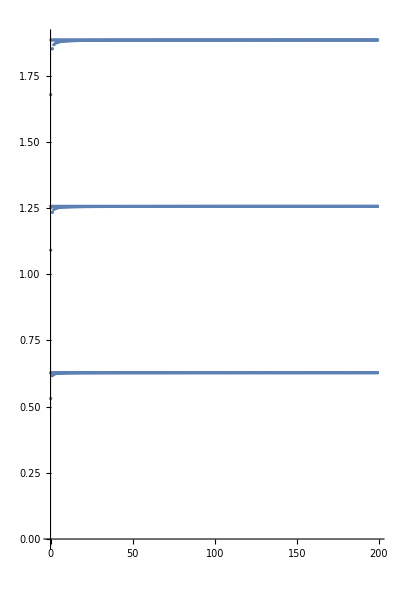

```mathematica
butterflyValues = {#[[2]], #[[1]]}&/@ points;
ListPlot[butterflyValues, PlotLegends->Automatic, InterpolationOrder->0, PlotRange->Full, AspectRatio->1.5]
```

## Bose Einstein Statistics

```mathematica
(*Trying to find a good point to stop the sum in the partition function BUT: mittlere Besetzungszahl pro Teilchen!*)
```

## Wave function

```mathematica
(*Not needed for the Energy spectrum *)
```

```mathematica
Acoeff[block_, P_]=Subscript["𝒜", block][P];
allBlocks[N_, barN_] := DeleteDuplicates[Flatten[Permutations[#]&/@(PadRight[#, barN+1]&/@IntegerPartitions[N, barN+1]),1]]
χ[wellN_, ds_, ys_] := Module[{ Ep}, (Ep ={k,-k}; ∑_(ne=1)^(Dimensions[Ep][[1]]) (-Exp[-ⅈ k L])^If[Refine[Sign[Ep[[ne]]],k>0]==1,0,1](makeCoef[ wellN,ds, ys]/.k->Ep[[ne]])Exp[ⅈ Ep[[ne]] x])]
Ψ[ds_,ys_, barN_] := Module[{bN, allB, N, dels, curWell, barHs, barPos,LL}, (N=1;allB=allBlocks[N, barN];
barPos=ys;
(*barPos = Flatten[{y0,ys,Symbol["y"<>ToString[barN+1]]}];LL=2(π/k)Ceiling[L (k/(2 π))];Total[(curWell=#;χ[curWell, ds, ys](Product[HeavisideTheta[-barPos[[i+1]]+Sign[x]Mod[Abs[x], LL]], {i, 0, curWell-1}]Product[HeavisideTheta[barPos[[i+1]]-Sign[x]Mod[Abs[x], LL]], {i, curWell,barN+1}]))&/@Range[1,barN+1]]*)
HeavisideTheta[x+L/2]HeavisideTheta[-x+L/2]Total[(curWell=#;χ[curWell, ds, ys]Product[HeavisideTheta[-barPos[[i]]+x], {i, 1, curWell-1}]Product[HeavisideTheta[barPos[[i]]-x], {i, curWell,barN}])&/@Range[1,barN+1]])]
```

```mathematica
onePartWF[x_] =Ψ[ds,ys, numBar]//.Flatten[{specificRules, δ->Delta,γ->GGamma, randRulesAllDelta, #}]&/@rootPt;
```

```mathematica
rootList = (k/.#)&/@rootPt;
```

```mathematica
ntoplot=Range[1,Length[rootPt]](*{numBar,2*numBar}*);

Flatten[{specificRules, δ->Delta, γ->GGamma,randRulesAllDelta, rootPt}];
nrmSymb = calcNorm[ds, ys];
normSqr = (nrmSymb//.Flatten[{δ->Delta,γ->GGamma,{randRulesAllDelta},{specificRules}, {#}}])&/@rootPt;
normSqr[[ntoplot]];
(*NIntegrate[Abs[onePartWF[x][[#]]]^2/1, Evaluate[ ({x, -L/2, L/2}/.specificRules)]]&/@ntoplot*)
```

```mathematica
TGDensity=(Total@(Abs[onePartWF[x][[#]]]^2/normSqr[[#]]&/@ntoplot)[[1;;#]])&/@ntoplot;
```

```mathematica
SinglePartDensity = Abs[onePartWF[x][[#]]]^2/normSqr[[#]]&/@ntoplot;
```

```mathematica
d= 500
```

500

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

{{Symbol[],{}},{-5,Directive[GrayLevel[0],Thickness[Large]]},{5,Directive[GrayLevel[0],Thickness[Large]]}}

{k -> 0.62829339898213164000,k -> 0.62831853071795864769,k -> 1.2565867979650569137,k -> 1.2566370614359172954,k -> 1.8848801969495694545,k -> 1.8849555921538759431,k -> 2.5131735959364628957,k -> 2.5132741228718345908,k -> 3.1414669949265308700,k -> 3.1415926535897932385,k -> 3.7697603939205670095,k -> 3.7699111843077518862,k -> 4.3980537929193649458,k -> 4.3982297150257105338,k -> 5.0263471919237183092,k -> 5.0265482457436691815,k -> 5.6546405909344207293,k -> 5.6548667764616278292,k -> 6.2829339899522658342,k -> 6.2831853071795864769,k -> 6.9112273889780472509,k -> 6.9115038378975451246,k -> 7.5395207880125586047,k -> 7.5398223686155037723,k -> 8.1678141870565935194,k -> 8.1681408993334624200,k -> 8.7961075861109456168,k -> 8.7964594300514210677,k -> 9.4244009851764085171,k -> 9.4247779607693797154}

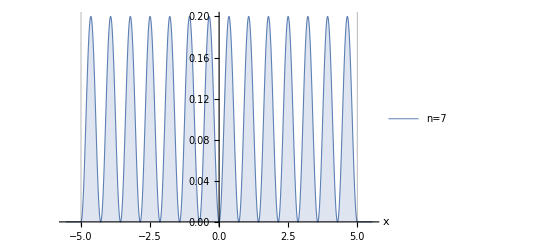

```mathematica
gridlns = Flatten[{randYs[[1;;-1]]/.{δ->Delta, γ->GGamma}, (-L/.specificRules)/2,(L/.specificRules)/2}];
glStyled=Flatten[{{gridlns[[#]], If[Mod[#,2]==1,{(*Dashed*)}, {(*Directive[Thick]*)}]}&/@ Range[1,Length[gridlns]-2],{{gridlns[[-2]], Directive[Black, Thick]}, {gridlns[[-1]], Directive[Black, Thick]}}},1]
legnd=Evaluate[ToString[#[[1]]]&/@rootPt]
SetOptions[Plot,BaseStyle->{FontFamily->"Times",FontSize->16, FontColor->Black}];
Plot[Evaluate[SinglePartDensity[[13]](*[[{6,7}]]*)],Evaluate[ ({x, (-L)/1.8, L/1.8}/.specificRules)],GridLines -> {glStyled, {}}, PlotRange->Full(*, PlotStyle->{Blue}*), Evaluated->True, PlotLegends->{"n=7", "n=14"}(*legnd[[ntoplot]]*), PlotPoints->150, AxesLabel->{x, ""}, PlotStyle->{Thickness[0.005], Thickness[0.002]}, Filling->Bottom, Ticks->Automatic, Exclusions->None]
```

```mathematica
1
```

1